## Routines

```mathematica
(*VFPdata=Import["/Users/hardindp/Dropbox/MinEnergyComputations/minEnergy/Graphics/qhull output/total.txt","Table"];*)
```

```mathematica
VFP[VFPdata_]:=Module[{VFstart,VFend, Vstart, Vend, Fstart, Fend,numPts,numFacets,dim, VertFacets,Verts,Facets,numNN},
numPts=VFPdata[[1,1]];
VFstart=2;VFend=numPts+1;
dim=VFPdata[[VFend+1,1]];
VertFacets= Map[Drop[#,1]+1&,VFPdata[[VFstart;;VFend]]];
numNN= Map[ #[[1]]&,VFPdata[[VFstart;;VFend]]];
Vstart=VFend+3;
 Vend=Vstart+numPts-1;
numFacets=VFPdata[[Vend+1,1]];
Verts=VFPdata[[Vstart;;Vend]];
Fstart=Vend+2;
Fend=Fstart+VFPdata[[Vend+1,1]]-1;
Facets=Map[Drop[#,1]+1&,VFPdata[[Fstart;;Fend]]];
{{dim, numPts,numFacets},numNN,VertFacets,Verts,Facets}];
```

```mathematica
GetVertFacets[VFPfile_]:=VFPfile[[3]]
GetVerts[VFPfile_]:=VFPfile[[4]]
GetFacets[VFPfile_]:=VFPfile[[5]]
GetnumNN[VFPfile_]:=VFPfile[[2]]
NumVerts[VFPfile_]:= Length[VFPfile[[4]]]
```

```mathematica
CircCenter[{u1_,u2_,u3_}]:=Module[{c1,c2,c3,v},
{c1,c2}={-((-1+u1.u2+u1.u3-u2.u3) (-1+u2.u3))/(-3+(u1.u2)^2+2 u1.u3+(u1.u3-u2.u3)^2+2 u2.u3-2 u1.u2 (-1+u1.u3+u2.u3)),((-1+u1.u3) (1-u1.u2+u1.u3-u2.u3))/(-3+(u1.u2)^2+2 u1.u3+(u1.u3-u2.u3)^2+2 u2.u3-2 u1.u2 (-1+u1.u3+u2.u3))};
c3=1-c1-c2;
v={c1,c2,c3}.{u1,u2,u3};
v=v/Sqrt[v.v]]
```

```mathematica
NextFacet[ptIndex_,OtherPtIndex_,Facets_,currFacetIndex_]:= Module[{nextFacet,nextPtIndex},
nextFacet=Complement[Position[Facets,OtherPtIndex][[All,1]],{currFacetIndex}][[1]];
nextPtIndex=Complement[Facets[[nextFacet]],{ptIndex,OtherPtIndex}][[1]];
{nextFacet,nextPtIndex}]
```

```mathematica
VorCell[VFPfile_,ptIndex_]:=Module[{VorVerts,theFacets, theEdge},
theFacets=GetFacets[VFPfile][[GetVertFacets[VFPfile][[ptIndex]]]];
Map[CircCenter,Partition[GetVerts[VFPfile][[Flatten[theFacets]]],3] ]]
```

```mathematica
VorCelltoTris[verts_,pt_]:={EdgeForm[],Switch[Length[verts],5,RGBColor[0,0,1],6,RGBColor[0,1,0],7,RGBColor[1,0,0],_,White],Triangle[Append[Table[{verts[[k]],verts[[k+1]],pt},{k,1,Length[verts]-1}],{verts[[-1]],verts[[1]],pt}]],{Black,Line[Append[verts,verts[[1]]]]}}
```

```mathematica
VorCelltoPolygon[verts_,pt_]:={Switch[Length[verts],5,RGBColor[0,0,1],6,RGBColor[0,1,0],7,RGBColor[1,0,0],_,White],Polygon[verts],{Black,Line[Append[verts,verts[[1]]]]}}
```

```mathematica
VorCelltoPolygon[verts_,pt_]:={Switch[Length[verts],5,RGBColor[0,0,1],6,RGBColor[0,1,0],7,RGBColor[1,0,0],_,White],Polygon[verts]}
```

```mathematica
VorCells[VFPFiles_]:=Table[VorCell[VFPFiles,k],{k,1,VFPFiles[[1,2]]}]
```

```mathematica
VorGraph[VFPFiles_]:=Table[VorCelltoPolygon[VorCell[VFPFiles,k],GetVerts[VFPFiles][[k]]],{k,1,NumVerts[VFPFiles]}];
```

```mathematica
PlotThisFile[VFPData_]:= Module[{path,VFPFiles},
VFPFiles=VFP[VFPData];
Graphics3D[ {Thickness[.000001],PointSize[.001],VorGraph[VFPFiles],Black,Map[Point,1.003*GetVerts[VFPFiles]]},Boxed->False]
]
```

## Area

### Areas

```mathematica
VFPFiles=VFP[VorFiles[[1]]];
```

```mathematica
vor = VorGraph[VFPFiles];
```

```mathematica
areas=Map[Area[vor[[#,2]]]&,Range[NumVerts[VFPFiles]]];
```

```mathematica
meanArea=Mean[areas]
varianceArea=Variance[areas]
```

0.0125314

0.0000423448

```mathematica
pens=Extract[VorCells[VFPFiles],Position[Length/@VorCells[VFPFiles],5]];
hexs=Extract[VorCells[VFPFiles],Position[Length/@VorCells[VFPFiles],6]];
heps=Extract[VorCells[VFPFiles],Position[Length/@VorCells[VFPFiles],7]];
```

```mathematica
{numPen=Length[pens],numHex=Length[hexs],numHep=Length[heps]}
```

{274,317,202}

```mathematica
penArea=Map[Area[Polygon[pens[[#]]]]&,Range[Length[pens]]];
hexArea=Map[Area[Polygon[hexs[[#]]]]&,Range[Length[hexs]]];
hepArea=Map[Area[Polygon[heps[[#]]]]&,Range[Length[heps]]];
```

```mathematica
{meanPenArea=Mean[penArea],meanHexArea=Mean[hexArea],meanHepArea=Mean[hepArea]}
```

{0.00951989,0.0123517,0.0159434}

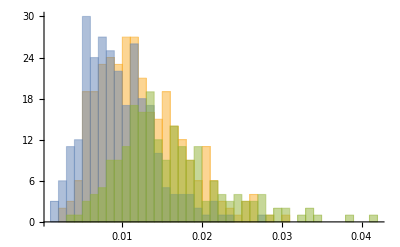

```mathematica
Histogram[{hexArea,penArea,hepArea},50]
```

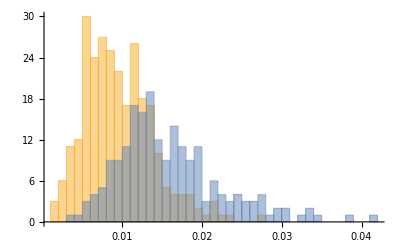

```mathematica
Histogram[{penArea, hepArea},50]
```

## 1k Comparison

### Import

```mathematica
ConjGrad1kPath = StringJoin[ NotebookDirectory[],"/may22compare1k/may22test1kConjGrad/"];
Grad1kPath=StringJoin[ NotebookDirectory[],"/may22compare1k/may22test1kGradDes/"];
ConjGrad1kAllFiles = FileNames["total*.txt",ConjGrad1kPath];
Grad1kAllFiles= FileNames["total*.txt",Grad1kPath];
```

```mathematica
numFiles=Length[ConjGrad1kAllFiles];
```

```mathematica
ConjGrad1kFiles=Table[Import[ConjGrad1kPath<>"total"<>ToString[i]<>".txt","Table"],{i,1,numFiles}];
Grad1kFiles=Table[Import[Grad1kPath<>"total"<>ToString[i]<>".txt","Table"],{i,1,numFiles}];
```

```mathematica
ConjGrad1kFiles[[1]];
```

### Plot

#### Voronoi Diagram

```mathematica
PlotThisFile[Grad1kFiles[[-1]]];
```

```mathematica
ConjGrad1kPlots = Table[PlotThisFile[ConjGrad1kFiles[[i]]],{i,1,numFiles}];
```

```mathematica
Grad1kPlots = Table[PlotThisFile[Grad1kFiles[[i]]],{i,1,numFiles}];
```

```mathematica
ConjGrad1kAnimate=ListAnimate[ConjGrad1kPlots,AnimationRate->.8];
```

```mathematica
Grad1kAnimate=ListAnimate[Grad1kPlots,AnimationRate->.8];
```

#### Energy

```mathematica
ConjGrad1kEnergy=Drop[Import[ConjGrad1kPath<>"epsFile.txt","Table"][[All,5]],1];
Grad1kEnergy=Drop[Import[Grad1kPath<>"epsFile.txt","Table"][[All,5]],1];
```

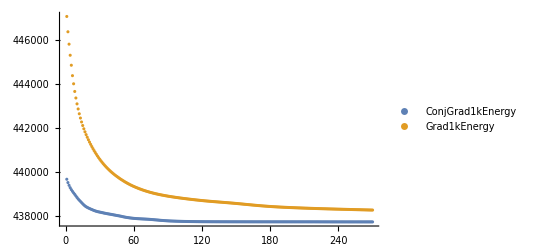

```mathematica
ListPlot[{Labeled[Drop[ConjGrad1kEnergy,30],"ConjGrad1kEnergy"],Labeled[Drop[Grad1kEnergy,30],"Grad1kEnergy"]},PlotRange->All,PlotLegends->{"ConjGrad1kEnergy","Grad1kEnergy"}]
```

## 3k Comparison

### Import

```mathematica
ConjGrad3kPath = StringJoin[ NotebookDirectory[],"/may22compare3k/may22test3kConjGrad/"];
Grad3kPath=StringJoin[ NotebookDirectory[],"/may22compare3k/may22test3kGradDes/"];
ConjGrad3kAllFiles = FileNames["total*.txt",ConjGrad3kPath];
Grad3kAllFiles= FileNames["total*.txt",Grad3kPath];
```

```mathematica
numFiles=Length[ConjGrad3kAllFiles];
```

```mathematica
ConjGrad3kFiles=Table[Import[ConjGrad3kPath<>"total"<>ToString[i]<>".txt","Table"],{i,1,numFiles}];
Grad3kFiles=Table[Import[Grad3kPath<>"total"<>ToString[i]<>".txt","Table"],{i,1,numFiles}];
```

```mathematica
ConjGrad3kFiles[[1]];
```

### Plot

#### Voronoi Diagram

```mathematica
PlotThisFile[Grad3kFiles[[-1]]];
```

```mathematica
ConjGrad3kPlots = Table[PlotThisFile[ConjGrad3kFiles[[i]]],{i,1,numFiles}];
```

```mathematica
Grad3kPlots = Table[PlotThisFile[Grad3kFiles[[i]]],{i,1,numFiles}];
```

```mathematica
ConjGrad3kAnimate=ListAnimate[ConjGrad3kPlots,AnimationRate->.8,ViewPoint];
```

```mathematica
Grad3kAnimate=ListAnimate[Grad3kPlots,AnimationRate->.8];
```

#### Energy

```mathematica
ConjGrad3kEnergy=Drop[Import[ConjGrad3kPath<>"epsFile.txt","Table"][[All,5]],1];
Grad3kEnergy=Drop[Import[Grad3kPath<>"epsFile.txt","Table"][[All,5]],1];
```

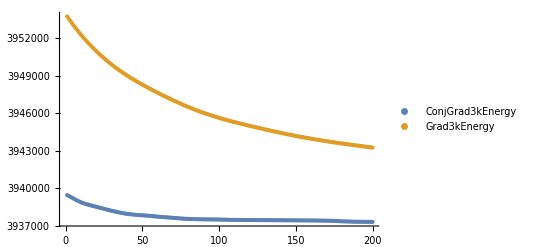

```mathematica
ListPlot[{Labeled[Drop[ConjGrad3kEnergy,100],"ConjGrad3kEnergy"],Labeled[Drop[Grad3kEnergy,100],"Grad3kEnergy"]},PlotLegends->{"ConjGrad3kEnergy","Grad3kEnergy"}]
```